# Authorship Classification

## Data

Import the data set

```mathematica
text=Import["https://archive.ics.uci.edu/ml/machine-learning-databases/00217/C50.zip","*.txt"];
```

```mathematica
directories = Map[DirectoryName,Import["https://archive.ics.uci.edu/ml/machine-learning-databases/00217/C50.zip"]];
```

```mathematica
authors = FileNameTake[#,-1]&/@directories;
```

Divide the data into training and validation sets

```mathematica
trainingText=text[[1;;2500]];
trainingAuthors= authors[[1;;2500]];
testText = text[[2501;;]];
testAuthors = authors[[2501;;]];
```

The full-text training and testing sets are:

```mathematica
fullTrainingArticles = Thread[trainingText->trainingAuthors];
```

```mathematica
fullTestArticles = Thread[testText->testAuthors];
```

We need to format the training and validation sets for input to different models

```mathematica
trainingTextSentences = TextSentences[trainingText];
testTextSentences=TextSentences[testText];
threadedTrainingText = Thread[trainingTextSentences-> trainingAuthors];
threadedTestText = Thread[testTextSentences->testAuthors];
```

```mathematica
transform[d_]:=MapThread[#1->#2&,{d[[1]],Table[d[[2]],Length[d[[1]]]]}];
```

```mathematica
trainingTextSmaller=Flatten[transform/@threadedTrainingText];
testTextSmaller = Flatten[transform/@threadedTestText];
```

```mathematica
trainingTextAssociation=trainingTextSmaller//.x:{__Rule}:>Association[x];
testTextAssociation=testTextSmaller //.x:{__Rule} :> Association[x];
unionAuthors=Union@authors;
selectAuthor[author_]:=Select[trainingTextAssociation,#== author&];
```

```mathematica
selectTestAuthor[author_]:=Select[testTextAssociation,#== author&];
```

```mathematica
authorsText=selectAuthor/@unionAuthors;
authorsTestText = selectTestAuthor/@unionAuthors;
```

```mathematica
nonNormalizedTraining = Flatten@Normal@authorsText;
nonNormalizedTest = Flatten@Normal@authorsTestText;
```

```mathematica
normalizedTrainingText=Flatten@(RandomChoice[Normal@#,1500]&/@authorsText);
normalizedTestText=Flatten@(RandomChoice[Normal@#,1500]&/@authorsTestText);
```

```mathematica
fullTestSentences=Select[normalizedTestText,(StringLength@First[#]=!=0)&];
fullTrainingSentences=Select[normalizedTrainingText,(StringLength@First[#]=!=0)&];
KeySort@Counts[StringLength/@Keys[fullTrainingSentences]];
```

The reduced training and testing set with sentences are:

```mathematica
reducedTrainingSentences=RandomSample[fullTrainingSentences,16];
reducedTestSentences=RandomSample[fullTestSentences,16];
```

The reduced training and testing set with full-text are:

```mathematica
reducedTrainingArticles = RandomSample[fullTrainingArticles,100];
reducedTestArticles=RandomSample[fullTestArticles,100];
```

```mathematica
groupedArticles=MapAt[{#,CreateUUID[]}&,threadedTestText,{All,2}];
groupedSentences=Flatten[transform/@groupedArticles];
```

## Identification using Classifiers

We will use different methods to classify the data and compare their results.

## Classifiers that Process Full-Text Articles

We first feed full text articles to the classifier and use the Classify function:

```mathematica
cArticles = Classify[fullTrainingArticles]
```

ClassifierFunction[…]

Then we apply the resulting classifier to the Articles:

```mathematica
cArticlesMeasure=ClassifierMeasurements[cArticles,fullTestArticles]
```

ClassifierMeasurementsObject[…]

We measure the accuracy of the classifier:

```mathematica
cArticlesMeasure["Accuracy"]
```

0.664

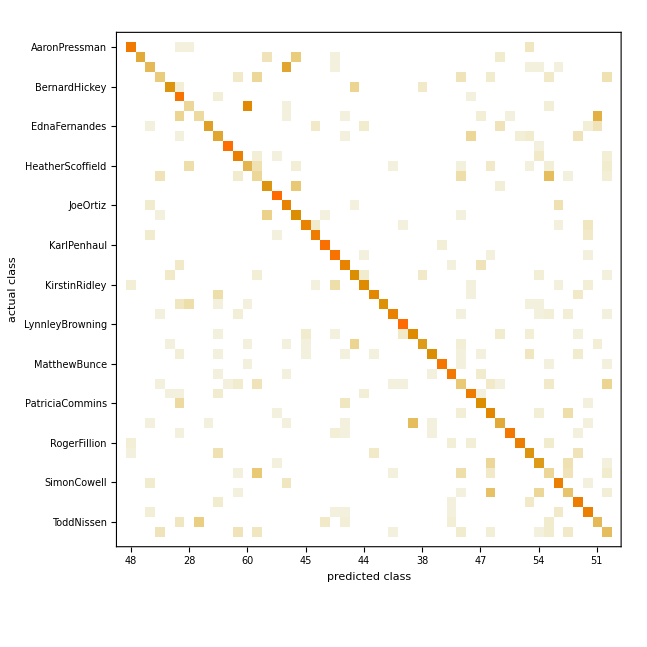

```mathematica
cArticlesMeasure["ConfusionMatrixPlot"]
```

## Classifiers that Process Sentences - Normalized (equal lengths)

```mathematica
cSentences=Classify[fullTrainingSentences]
```

ClassifierFunction[…]

```mathematica
cSentencesMeasure=ClassifierMeasurements[cSentences,fullTestSentences]
```

ClassifierMeasurementsObject[…]

```mathematica
cSentencesMeasure["Accuracy"]
```

0.390229

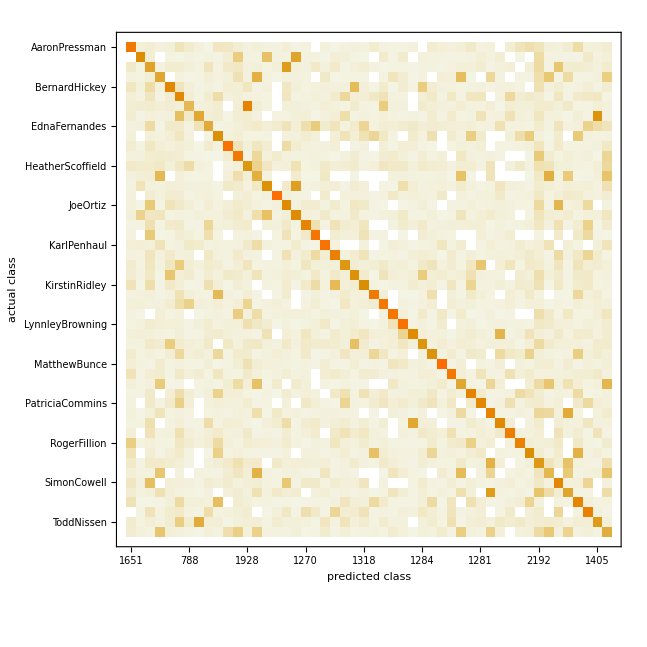

```mathematica
cSentencesMeasure["ConfusionMatrixPlot"]
```

## Classifiers that Process Non-Normalized Sentences

```mathematica
cNonNormalizedSentences=Classify[nonNormalizedTraining]
```

ClassifierFunction[…]

```mathematica
cNonNormalizedSentencesMeasure=ClassifierMeasurements[cNonNormalizedSentences,nonNormalizedTest]
```

ClassifierMeasurementsObject[…]

```mathematica
cNonNormalizedSentencesMeasure["Accuracy"]
```

0.398741

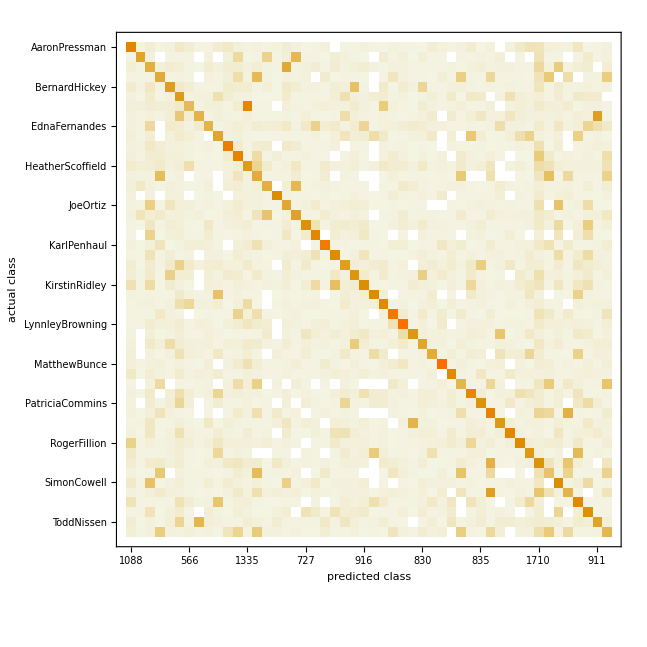

```mathematica
cNonNormalizedSentencesMeasure["ConfusionMatrixPlot"]
```

## PostProcessing of Results with Stochastic Model

```mathematica
resultNonNormalizedSentences=cNonNormalizedSentences[groupedSentences[[All,1]]]
```

{AaronPressman,AaronPressman,FumikoFujisaki,AaronPressman,AaronPressman,AaronPressman,TanEeLyn,BradDorfman,60125,BenjaminKangLim,BenjaminKangLim,BenjaminKangLim,BenjaminKangLim,BenjaminKangLim,JaneMacartney,BenjaminKangLim,PeterHumphrey}
 |  |  |  |

```mathematica
Counts[resultNonNormalizedSentences[[1;;31]]]
```

<|AaronPressman→14,FumikoFujisaki→1,TanEeLyn→1,BradDorfman→1,MatthewBunce→2,KarlPenhaul→1,KirstinRidley→1,MureDickie→1,RogerFillion→1,JoeOrtiz→2,HeatherScoffield→1,RobinSidel→1,BenjaminKangLim→1,AlanCrosby→1,SarahDavison→2|>

```mathematica
groupsByUniqueArticleIdentifier=groupedSentences[[All,2]]//Dataset;
```

```mathematica
grouped=Counts[groupsByUniqueArticleIdentifier[All,2]]
```

Dataset[<>]

```mathematica
groups=Values@Normal@grouped;
```

```mathematica
helperToSelectRange[indices_, range_]:= Select[indices, #⟦2⟧ < range&];

lookupCount[groupedSentenceTable_, nonNormalizedTestTable_, resultNonNormalizedSentencesTable_]:= Module[
	{range, numOfGroups, counts, s, start, end, groups, indices},
	(*range = Length[resultNonNormalizedSentencesTable];*)
	s = groupedSentenceTable[[All,2]]//Dataset;
	counts = Counts[s[All,2]];
	groups = Join[{1}, Values @ Normal @ counts];
	end = (FoldList[Plus, 0, groups]-1) ⟦3;;-1⟧;
	start = Join[{1}, end + 1] ⟦;;-2⟧;
	indices = Transpose[{start, end}];
	Counts /@ Table[resultNonNormalizedSentencesTable⟦indices⟦i,1⟧;;indices⟦i,2⟧⟧, {i, 1, Length @ indices}]
]

getHighestCount[assoc_]:= First @ First @ (Reverse @ SortBy[assoc, # &] /. Association -> List)
```

```mathematica
res=lookupCount[groupedSentences, nonNormalizedTest, resultNonNormalizedSentences]
```

{1}
 |  |  |  |

```mathematica
compare=getHighestCount/@res;
```

```mathematica
(r={testAuthors,compare}//Transpose)//Dataset
```

Dataset[<>]

```mathematica
check[str_]:= If[str⟦1⟧ == str⟦2⟧, True, False]
```

```mathematica
differentAuthors = {};
For[i = 1, i <= Length @ r, i++, 
	If[ check[r⟦i⟧], 
		Nothing, 
		AppendTo[differentAuthors, r⟦i⟧]
	];
]
```

```mathematica
Dataset@differentAuthors
```

Dataset[<>]

```mathematica
accuracy = N[1-(Length[differentAuthors]/Length[trainingAuthors])]
```

0.6536

## Using Feature Extraction

### Analyzing the Dataset

We are going to extract the features of the dataset to see how many dimensions are identified.

```mathematica
fe=FeatureExtraction[trainingText]
```

FeatureExtractorFunction[…]

```mathematica
fe["hello, this is my text"]
```

{-16.3762,-0.00666792,44.0829,103.751,53.1946,12.8302,31.5504,-19.3851,-14.0808,19.5329,-0.450887,17.9304,0.70113,-9.1441}

```mathematica
fe["I am writing a letter to myself"]
```

{82.3565,23.6788,-65.9087,-40.3814,-40.0484,19.2679,39.0711,10.1267,-13.2228,-18.5407,-11.1214,-1.34529,2.32226,-6.27461}

```mathematica
fe[testText[[1]]]
```

{0.429621,-21.4238,10.0077,14.6345,-4.36015,-1.48061,-14.0192,-1.25328,5.66613,2.35249,-1.01378,-1.59225,-1.96776,-0.631679}

```mathematica
fe[testText[[2]]]
```

{-12.1046,-15.8206,11.5188,10.8023,-2.14494,-0.576855,-16.1914,-0.965439,1.12874,0.148504,0.66751,1.97298,-0.962063,0.0498295}

Now we have an element fe which maps each text to a multi-dimensional numerical vector, in this particular case a 14-dimension vector.

Now we need to generate all the vectors for the testing set:

```mathematica
mappedTestText = fe[testText]
```

{1}
 |  |  |  |

Now we use DimensionReduction to reduce the number of dimensional features to 3 and 2, and we create a dimension reduction object dr which will allow us to map the testText data:

```mathematica
dr3 = DimensionReduction[mappedTestText,3,Method->"TSNE"]
```

DimensionReducerFunction[…]

```mathematica
dr2=DimensionReduction[mappedTestText,2,Method->"TSNE"]
```

DimensionReducerFunction[…]

We now reduce the testText to 3 dimensions”.1f

```mathematica
dr3D=dr3[mappedTestText];
```

```mathematica
dr2D=dr2[mappedTestText];
```

And now we plot it to see if there is any clustering.

First we need to resolve the labels for the authors.  We will do it by associating each text by an author with a color by grouping by author.

```mathematica
dr3Dp=Partition[dr3D,25]
```

{1}
 |  |  |  |

```mathematica
dr3Dp
```

{1}
 |  |  |  |

```mathematica
dr2Dp=Partition[dr2D,50];
```

```mathematica
dr2Dp
```

{1}
 |  |  |  |

```mathematica
Length@%
```

50

```mathematica
Dimensions@dr2Dp
```

{50,50,2}

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/jaimebuitrago/Dropbox/Jaime/Wolfram Summer School

```mathematica
Export["plotSetClas2.mx",dr2Dp]
```

plotSetClas2.mx

```mathematica
plotSetClas2=Import["/Users/jaimebuitrago/Dropbox/Jaime/Wolfram Summer School/plotSetClas.mx"]
```

{1}
 |  |  |  |

```mathematica
Manipulate[ListPlot[plotSetClas2[[n]],PlotLabel->"Neural Network",PlotRange->{{-50,50},{-50,50}},PlotTheme->"Marketing",PlotStyle->Blue],{n,1,25,1},"Author"]
```

And we generate a 3D plot of the reduced dimension test set, where each color represents an author:

```mathematica
plot3D=ListPointPlot3D[dr3Dp,Filling->Bottom]
```

-Graphics3D-

This is the 2D Plot:

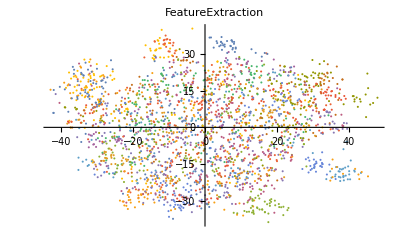

```mathematica
plot2DFeatExtr=ListPlot[dr2Dp,PlotLabel->"FeatureExtraction"]
```

Let’s look at the plot one author at a time:

```mathematica
plot2=ListPointPlot3D[dr3Dp[[#]],Filling->Bottom ]&/@Range[25]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

## Classification using Neural Networks

## Neural Network Elements

```mathematica
featureExtractor2=NetModel["GloVe 100-Dimensional Word Vectors Trained on Wikipedia and Gigaword 5 Data"]
```

EmbeddingLayer[<>]

Layers to try:
“LSTM1”→ LongShortTermMemoryLayer[50]
“GRU1”->GatedRecurrentLayer[100]
“Sequence”→ SequenceLastLayer[]
“Linear”→ LinearLayer[]
“SoftMax”→ SoftmaxLayer[]

```mathematica
net=NetChain[<|"Feature Extractor" -> featureExtractor2,"LSTM1"-> LongShortTermMemoryLayer[50],"GRU1"->GatedRecurrentLayer[100],"Pooling"-> PoolingLayer[100],"Linear"->LinearLayer[],"SoftMax"-> SoftmaxLayer[]|>,"Output"->NetDecoder[{"Class",unionAuthors}]]
```

NetChain[<>]

## Neural Network Training

```mathematica
trained=NetTrain[net,fullTrainingArticles,All,ValidationSet->fullTestArticles,LearningRateMultipliers->{"Feature Extractor"->0,_->1},MaxTrainingRounds->20,TargetDevice->"CPU"]
```

NetTrain::nninit: Cannot train net: unspecified or partially specified shape for array "Weights" of layer "Linear".

$Failed

## Training Results

```mathematica
trainedBest=trained;
```

```mathematica
trainedBest["TrainedNet"];
```

```mathematica
trainedBest["TrainingNet"];
```

```mathematica
trainedBest["ErrorRateEvolutionPlot"];
```

```mathematica
trainedBest["FinalRoundErrorRate"];
```

```mathematica
trainedBest["TotalTrainingTime"];
```

```mathematica
trainedBest["Properties"];
```

## Neural Network Pruning

```mathematica
trainedVectorizer = NetDrop[trainedBest["TrainedNet"],-2]
```

NetDrop::netarg1: First argument should be a valid net.

$Failed

```mathematica
trainedBest["TrainedNet"]
```

$Failed[TrainedNet]

## Using the Pruned Neural Network as a Vectorizer

```mathematica
features=trainedVectorizer[fullTestArticles[[All,1]]]
```

$Failed[fullTestArticles⟦All,1⟧]

## Reducing the Dimension of the Resulting Vector Space

```mathematica
dimReduction=DimensionReduction[features,2,Method->"TSNE"]
```

DimensionReduction::mlbddata: The data is not formatted correctly.

DimensionReduction[$Failed[fullTestArticles⟦All,1⟧],2,Method→TSNE]

```mathematica
drx=dimReduction[features];
```

```mathematica
plotSet = Partition[drx,25];
```

## Generate Vector Plot

```mathematica
plot2DNeuralNetwork=ListPlot[plotSet,PlotLabel->"Neural Network"];
```

DimensionReduction::mlbddata: The data is not formatted correctly.

ListPlot::lpn: DimensionReduction[$Failed[fullTestArticles⟦All,1⟧],2.,Method→TSNE][] is not a list of numbers or pairs of numbers.

DimensionReduction::mlbddata: The data is not formatted correctly.

General::stop: Further output of DimensionReduction::mlbddata will be suppressed during this calculation.

ListPlot::lpn: DimensionReduction[$Failed[fullTestArticles⟦All,1⟧],2.,Method→TSNE][] is not a list of numbers or pairs of numbers.

DimensionReduction::mlbddata: The data is not formatted correctly.

General::stop: Further output of DimensionReduction::mlbddata will be suppressed during this calculation.

ListPlot::lpn: DimensionReduction[$Failed[fullTestArticles⟦All,1⟧],2.,Method→TSNE][] is not a list of numbers or pairs of numbers.

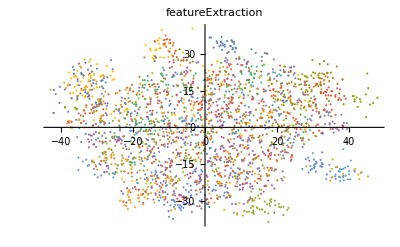

```mathematica
GraphicsRow[{plot2DFeatExtr,plot2DNeuralNetwork},Frame->All,ImageSize->800]
```

## Visualization

```mathematica
plotx=Import["/Users/jaimebuitrago/Dropbox/Jaime/Wolfram Summer School/plotSet.mx"];
```

```mathematica
NNMan=Manipulate[ListPlot[plotx[[n]],PlotLabel->"Neural Network",PlotRange->{{-50,50},{-50,50}},PlotTheme->"Marketing",PlotStyle->Blue,ImageSize->Full],{n,1,25,1},"Author",ContentSize->{600, 460}]
```

```mathematica
plotSetClas=Import["/Users/jaimebuitrago/Dropbox/Jaime/Wolfram Summer School/plotSetClas.mx"];
```

```mathematica
ClasMan=Manipulate[ListPlot[plotSetClas[[n]],PlotLabel->"Classifier",PlotRange->{{-50,50},{-50,50}},PlotTheme->"Marketing",PlotStyle->Blue,ImageSize->Full],{n,1,25,1},"Author",ContentSize->{600, 460}]
```

```mathematica
TabView[{ClasMan,NNMan}]
```

12